```mathematica
rules=Solve[{
eps-e,
f*(2pi)^4+g*(2pi)^3+h*(2pi)^2+i*(2pi)+j-eps,
d,
4f *(2 pi)^3+3g *(2 pi)^2+2h *(2pi )+i,
2c-12f*(2pi)^2-6g*(2pi)-2h,
a*beta^4+b beta^3+c beta^2+d beta+e-eps,
f*beta^4+g beta^3+h beta^2+i beta+j-eps,
4a beta^3+3b beta^2+2c beta+d,
4f beta^3+3g beta^2+2h beta+i,
12a beta^2+6b beta+2c-12f beta^2-6g beta-2h
}=={0,0,0,0,0,delta,delta,0,0,0},{a,b,c,d,e,f,g,h,i,j}]
```

{}

```mathematica
coef={a,b,c,d,e,f,g,h,i,j}/.rules
```

{a,b,c,d,e,f,g,h,i,j}

```mathematica
A={x^4,x^3,x^2,x,1}.coef[[1]][[1;;5]]
```

eps+(2 (beta^3 delta-beta^2 delta pi-18 beta delta pi^2+24 delta pi^3) x^2)/(beta^2 (beta-2 pi)^2 (beta+2 pi))-(4 (beta^2 delta pi-14 beta delta pi^2+16 delta pi^3) x^3)/(beta^3 (beta-2 pi)^2 (beta+2 pi))-((beta^3 delta-4 beta^2 delta pi+24 beta delta pi^2-24 delta pi^3) x^4)/(beta^4 (beta-2 pi)^2 (beta+2 pi))

```mathematica
Plot[Replace[A, {{beta-> Pi}, {delta->0.5/Pi}, {eps->0}, {pi->Pi}}],{x,0,2Pi}]
```

-Graphics-

```mathematica
B={x^4,x^3,x^2,x,1}.coef[[1]][[6;;10]]
```

-(-beta^3 eps+2 beta^2 eps pi+8 beta delta pi^2+4 beta eps pi^2-8 delta pi^3-8 eps pi^3)/((beta-2 pi)^2 (beta+2 pi))+(2 (beta^2 delta-beta delta pi+6 delta pi^2) x^2)/(beta (beta-2 pi)^2 (beta+2 pi))-(4 delta pi x^3)/(beta^2 (beta-2 pi)^2)-((beta delta-4 delta pi) x^4)/(beta^2 (beta-2 pi)^2 (beta+2 pi))

```mathematica
Solve[{
a*beta^4+b beta^3+c beta^2+d beta+e-eps,
4a beta^3+3b beta^2+2c beta+d,
j-eps,
i,
a*(beta/2)^4+b (beta/2)^3+c (beta/2)^2+d (beta/2)+e-(f*(beta/2)^4+g (beta/2)^3+h (beta/2)^2+i (beta/2)+j),
a*(beta/2+pi)^4+b (beta/2+pi)^3+c (beta/2+pi)^2+d (beta/2+pi)+e-(f*(beta/2-pi)^4+g (beta/2-pi)^3+h (beta/2-pi)^2+i (beta/2-pi)+j),
4a (beta/2)^3+3b (beta/2)^2+2c (beta/2)+d -(4f (beta/2)^3+3g (beta/2)^2+2h (beta/2)+i),
4a (beta/2+pi)^3+3b (beta/2+pi)^2+2c (beta/2+pi)+d -(4f (beta/2-pi)^3+3g (beta/2-pi)^2+2h (beta/2-pi)+i),
12a (beta/2)^2+6b (beta/2)+2c-12f (beta/2)^2-6g (beta/2)-2h,
12a (beta/2+pi)^2+6b (beta/2+pi)+2c-12f (beta/2-pi)^2-6g (beta/2-pi)-2h
}=={delta,0,0,0,0,0,0,0,0,0},{a,b,c,d,e,f,g,h,i,j}]
```

{}

```mathematica
rules=Solve[{
eps-e,
f*(2pi)^4.5+g*(2pi)^3+h*(2pi)^2+i*(2pi)+j-eps,
d,
4.5f *(2 pi)^3.5+3g *(2 pi)^2+2h *(2pi )+i,
2c-13.5f*(2pi)^2.5-6g*(2pi)-2h,
a*beta^4.5+b beta^3+c beta^2+d beta+e-eps,
f*beta^4.5+g beta^3+h beta^2+i beta+j-eps,
4.5a beta^3.5+3b beta^2+2c beta+d,
4.5f beta^3.5+3g beta^2+2h beta+i,
13.5a beta^2.5+6b beta+2c-13.5f beta^2.5-6g beta-2h
}=={0,0,0,0,0,delta,delta,0,0,0},{a,b,c,d,e,f,g,h,i,j}]
```

{{a→(4. (-0.166667 beta^3.5+1. beta^2.5 pi-2.82843 beta pi^2.5+1.88562 pi^3.5) (0.125 beta^9.5 delta pi-0.875 beta^8.5 delta pi^2+2.25 beta^7.5 delta pi^3-2.5 beta^6.5 delta pi^4+1. beta^5.5 delta pi^5))/(beta^2.5 (1. beta-2. pi) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),b→-((1.5 (0.00347222 beta^17. delta pi-0.0720486 beta^16. delta pi^2-0.00368285 beta^15.5 delta pi^2.5+0.635417 beta^15. delta pi^3+0.127672 beta^14.5 delta pi^3.5-3.15972 beta^14. delta pi^4-1.48296 beta^13.5 delta pi^4.5+9.81944 beta^13. delta pi^5+8.97633 beta^12.5 delta pi^5.5-19.8333 beta^12. delta pi^6-32.9983 beta^11.5 delta pi^6.5+26.0556 beta^11. delta pi^7+78.646 beta^10.5 delta pi^7.5-21.4444 beta^10. delta pi^8-124.294 beta^9.5 delta pi^8.5+10. beta^9. delta pi^9+129.165 beta^8.5 delta pi^9.5-2. beta^8. delta pi^10-84.5385 beta^7.5 delta pi^10.5+31.427 beta^6.5 delta pi^11.5-5.02831 beta^5.5 delta pi^12.5))/(beta^1. (-0.5 beta+1. pi) (0.0625 beta^4-0.5 beta^3 pi+1.5 beta^2 pi^2-2. beta pi^3+1. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),c→-((25.4558 (0.00245523 beta^17. delta pi-0.0491046 beta^16. delta pi^2-0.0104167 beta^15.5 delta pi^2.5+0.412479 beta^15. delta pi^3+0.236111 beta^14.5 delta pi^3.5-1.9249 beta^14. delta pi^4-2.23611 beta^13.5 delta pi^4.5+5.49972 beta^13. delta pi^5+11.8889 beta^12.5 delta pi^5.5-9.89949 beta^12. delta pi^6-39.6667 beta^11.5 delta pi^6.5+10.9994 beta^11. delta pi^7+87.1111 beta^10.5 delta pi^7.5-6.91393 beta^10. delta pi^8-127.556 beta^9.5 delta pi^8.5+1.88562 beta^9. delta pi^9+122.667 beta^8.5 delta pi^9.5-73.7778 beta^7.5 delta pi^10.5+24.8889 beta^6.5 delta pi^11.5-3.55556 beta^5.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),d→0.,e→1. eps,f→-((0.0589256 (1. beta^9.5 delta pi-7. beta^8.5 delta pi^2+18. beta^7.5 delta pi^3-20. beta^6.5 delta pi^4+8. beta^5.5 delta pi^5))/(0.0147314 beta^14. pi-0.176777 beta^13. pi^2+0.0625 beta^12.5 pi^2.5+0.707107 beta^12. pi^3-0.291667 beta^11.5 pi^3.5-1.17851 beta^11. pi^4+0.166667 beta^10.5 pi^4.5+0.707107 beta^10. pi^5+1. beta^9.5 pi^5.5-1.66667 beta^8.5 pi^6.5+0.666667 beta^7.5 pi^7.5)),g→(33.9411 (0.00491046 beta^15. delta pi-0.0601532 beta^14. delta pi^2-0.00520833 beta^13.5 delta pi^2.5+0.306904 beta^13. delta pi^3+0.0347222 beta^12.5 delta pi^3.5-0.834779 beta^12. delta pi^4+0.0625 beta^11.5 delta pi^4.5+1.27672 beta^11. delta pi^5-1.31944 beta^10.5 delta pi^5.5-1.04102 beta^10. delta pi^6+5.55556 beta^9.5 delta pi^6.5+0.353553 beta^9. delta pi^7-11.7778 beta^8.5 delta pi^7.5+13.8889 beta^7.5 delta pi^8.5-8.66667 beta^6.5 delta pi^9.5+2.22222 beta^5.5 delta pi^10.5))/((1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),h→-((67.8823 (0.000920712 beta^17. delta pi-0.00368285 beta^16. delta pi^2-0.00390625 beta^15.5 delta pi^2.5-0.0552427 beta^15. delta pi^3+0.0260417 beta^14.5 delta pi^3.5+0.559793 beta^14. delta pi^4+0.09375 beta^13.5 delta pi^4.5-2.28337 beta^13. delta pi^5-1.5625 beta^12.5 delta pi^5.5+5.12652 beta^12. delta pi^6+7.04167 beta^11.5 delta pi^6.5-6.65859 beta^11. delta pi^7-16.25 beta^10.5 delta pi^7.5+4.71405 beta^10. delta pi^8+20. beta^9.5 delta pi^8.5-1.41421 beta^9. delta pi^9-9.66667 beta^8.5 delta pi^9.5-5. beta^7.5 delta pi^10.5+8. beta^6.5 delta pi^11.5-2.66667 beta^5.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),i→(33.9411 (0.0073657 beta^17. delta pi^2-0.0883883 beta^16. delta pi^3-0.03125 beta^15.5 delta pi^3.5+0.397748 beta^15. delta pi^4+0.395833 beta^14.5 delta pi^4.5-0.648181 beta^14. delta pi^5-1.91667 beta^13.5 delta pi^5.5-0.883883 beta^13. delta pi^6+3.58333 beta^12.5 delta pi^6.5+5.65685 beta^12. delta pi^7+3.66667 beta^11.5 delta pi^7.5-10.1352 beta^11. delta pi^8-32.3333 beta^10.5 delta pi^8.5+8.48528 beta^10. delta pi^9+70.6667 beta^9.5 delta pi^9.5-2.82843 beta^9. delta pi^10-78.6667 beta^8.5 delta pi^10.5+45.3333 beta^7.5 delta pi^11.5-10.6667 beta^6.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),j→(1. (0.0208333 beta^19. eps pi-0.458333 beta^18. eps pi^2+0.0883883 beta^17.5 eps pi^2.5-0.25 beta^17. delta pi^3+4.33333 beta^17. eps pi^3-1.29636 beta^16.5 eps pi^3.5+3.66667 beta^16. delta pi^4-23.3333 beta^16. eps pi^4+1.06066 beta^15.5 delta pi^4.5+7.89603 beta^15.5 eps pi^4.5-23. beta^15. delta pi^5+79.3333 beta^15. eps pi^5-16.4992 beta^14.5 delta pi^5.5-24.513 beta^14.5 eps pi^5.5+80. beta^14. delta pi^6-177.333 beta^14. eps pi^6+111.251 beta^13.5 delta pi^6.5+32.9983 beta^13.5 eps pi^6.5-166.667 beta^13. delta pi^7+261.333 beta^13. eps pi^7-424.264 beta^12.5 delta pi^7.5+26.3987 beta^12.5 eps pi^7.5+208. beta^12. delta pi^8-245.333 beta^12. eps pi^8+999.378 beta^11.5 delta pi^8.5-184.791 beta^11.5 eps pi^8.5-144. beta^11. delta pi^9+133.333 beta^11. eps pi^9-1485.87 beta^10.5 delta pi^9.5+331.869 beta^10.5 eps pi^9.5+42.6667 beta^10. delta pi^10-32. beta^10. eps pi^10+1357.65 beta^9.5 delta pi^10.5-309.241 beta^9.5 eps pi^10.5-693.907 beta^8.5 delta pi^11.5+150.849 beta^8.5 eps pi^11.5+150.849 beta^7.5 delta pi^12.5-30.1699 beta^7.5 eps pi^12.5-1.51582×10^-13 beta^6.5 delta pi^13.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))}}

```mathematica
coef={a,b,c,d,e,f,g,h,i,j}/.rules
```

{{(4. (-0.166667 beta^3.5+1. beta^2.5 pi-2.82843 beta pi^2.5+1.88562 pi^3.5) (0.125 beta^9.5 delta pi-0.875 beta^8.5 delta pi^2+2.25 beta^7.5 delta pi^3-2.5 beta^6.5 delta pi^4+1. beta^5.5 delta pi^5))/(beta^2.5 (1. beta-2. pi) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),-((1.5 (0.00347222 beta^17. delta pi-0.0720486 beta^16. delta pi^2-0.00368285 beta^15.5 delta pi^2.5+0.635417 beta^15. delta pi^3+0.127672 beta^14.5 delta pi^3.5-3.15972 beta^14. delta pi^4-1.48296 beta^13.5 delta pi^4.5+9.81944 beta^13. delta pi^5+8.97633 beta^12.5 delta pi^5.5-19.8333 beta^12. delta pi^6-32.9983 beta^11.5 delta pi^6.5+26.0556 beta^11. delta pi^7+78.646 beta^10.5 delta pi^7.5-21.4444 beta^10. delta pi^8-124.294 beta^9.5 delta pi^8.5+10. beta^9. delta pi^9+129.165 beta^8.5 delta pi^9.5-2. beta^8. delta pi^10-84.5385 beta^7.5 delta pi^10.5+31.427 beta^6.5 delta pi^11.5-5.02831 beta^5.5 delta pi^12.5))/(beta^1. (-0.5 beta+1. pi) (0.0625 beta^4-0.5 beta^3 pi+1.5 beta^2 pi^2-2. beta pi^3+1. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),-((25.4558 (0.00245523 beta^17. delta pi-0.0491046 beta^16. delta pi^2-0.0104167 beta^15.5 delta pi^2.5+0.412479 beta^15. delta pi^3+0.236111 beta^14.5 delta pi^3.5-1.9249 beta^14. delta pi^4-2.23611 beta^13.5 delta pi^4.5+5.49972 beta^13. delta pi^5+11.8889 beta^12.5 delta pi^5.5-9.89949 beta^12. delta pi^6-39.6667 beta^11.5 delta pi^6.5+10.9994 beta^11. delta pi^7+87.1111 beta^10.5 delta pi^7.5-6.91393 beta^10. delta pi^8-127.556 beta^9.5 delta pi^8.5+1.88562 beta^9. delta pi^9+122.667 beta^8.5 delta pi^9.5-73.7778 beta^7.5 delta pi^10.5+24.8889 beta^6.5 delta pi^11.5-3.55556 beta^5.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),0.,1. eps,-((0.0589256 (1. beta^9.5 delta pi-7. beta^8.5 delta pi^2+18. beta^7.5 delta pi^3-20. beta^6.5 delta pi^4+8. beta^5.5 delta pi^5))/(0.0147314 beta^14. pi-0.176777 beta^13. pi^2+0.0625 beta^12.5 pi^2.5+0.707107 beta^12. pi^3-0.291667 beta^11.5 pi^3.5-1.17851 beta^11. pi^4+0.166667 beta^10.5 pi^4.5+0.707107 beta^10. pi^5+1. beta^9.5 pi^5.5-1.66667 beta^8.5 pi^6.5+0.666667 beta^7.5 pi^7.5)),(33.9411 (0.00491046 beta^15. delta pi-0.0601532 beta^14. delta pi^2-0.00520833 beta^13.5 delta pi^2.5+0.306904 beta^13. delta pi^3+0.0347222 beta^12.5 delta pi^3.5-0.834779 beta^12. delta pi^4+0.0625 beta^11.5 delta pi^4.5+1.27672 beta^11. delta pi^5-1.31944 beta^10.5 delta pi^5.5-1.04102 beta^10. delta pi^6+5.55556 beta^9.5 delta pi^6.5+0.353553 beta^9. delta pi^7-11.7778 beta^8.5 delta pi^7.5+13.8889 beta^7.5 delta pi^8.5-8.66667 beta^6.5 delta pi^9.5+2.22222 beta^5.5 delta pi^10.5))/((1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),-((67.8823 (0.000920712 beta^17. delta pi-0.00368285 beta^16. delta pi^2-0.00390625 beta^15.5 delta pi^2.5-0.0552427 beta^15. delta pi^3+0.0260417 beta^14.5 delta pi^3.5+0.559793 beta^14. delta pi^4+0.09375 beta^13.5 delta pi^4.5-2.28337 beta^13. delta pi^5-1.5625 beta^12.5 delta pi^5.5+5.12652 beta^12. delta pi^6+7.04167 beta^11.5 delta pi^6.5-6.65859 beta^11. delta pi^7-16.25 beta^10.5 delta pi^7.5+4.71405 beta^10. delta pi^8+20. beta^9.5 delta pi^8.5-1.41421 beta^9. delta pi^9-9.66667 beta^8.5 delta pi^9.5-5. beta^7.5 delta pi^10.5+8. beta^6.5 delta pi^11.5-2.66667 beta^5.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))),(33.9411 (0.0073657 beta^17. delta pi^2-0.0883883 beta^16. delta pi^3-0.03125 beta^15.5 delta pi^3.5+0.397748 beta^15. delta pi^4+0.395833 beta^14.5 delta pi^4.5-0.648181 beta^14. delta pi^5-1.91667 beta^13.5 delta pi^5.5-0.883883 beta^13. delta pi^6+3.58333 beta^12.5 delta pi^6.5+5.65685 beta^12. delta pi^7+3.66667 beta^11.5 delta pi^7.5-10.1352 beta^11. delta pi^8-32.3333 beta^10.5 delta pi^8.5+8.48528 beta^10. delta pi^9+70.6667 beta^9.5 delta pi^9.5-2.82843 beta^9. delta pi^10-78.6667 beta^8.5 delta pi^10.5+45.3333 beta^7.5 delta pi^11.5-10.6667 beta^6.5 delta pi^12.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5)),(1. (0.0208333 beta^19. eps pi-0.458333 beta^18. eps pi^2+0.0883883 beta^17.5 eps pi^2.5-0.25 beta^17. delta pi^3+4.33333 beta^17. eps pi^3-1.29636 beta^16.5 eps pi^3.5+3.66667 beta^16. delta pi^4-23.3333 beta^16. eps pi^4+1.06066 beta^15.5 delta pi^4.5+7.89603 beta^15.5 eps pi^4.5-23. beta^15. delta pi^5+79.3333 beta^15. eps pi^5-16.4992 beta^14.5 delta pi^5.5-24.513 beta^14.5 eps pi^5.5+80. beta^14. delta pi^6-177.333 beta^14. eps pi^6+111.251 beta^13.5 delta pi^6.5+32.9983 beta^13.5 eps pi^6.5-166.667 beta^13. delta pi^7+261.333 beta^13. eps pi^7-424.264 beta^12.5 delta pi^7.5+26.3987 beta^12.5 eps pi^7.5+208. beta^12. delta pi^8-245.333 beta^12. eps pi^8+999.378 beta^11.5 delta pi^8.5-184.791 beta^11.5 eps pi^8.5-144. beta^11. delta pi^9+133.333 beta^11. eps pi^9-1485.87 beta^10.5 delta pi^9.5+331.869 beta^10.5 eps pi^9.5+42.6667 beta^10. delta pi^10-32. beta^10. eps pi^10+1357.65 beta^9.5 delta pi^10.5-309.241 beta^9.5 eps pi^10.5-693.907 beta^8.5 delta pi^11.5+150.849 beta^8.5 eps pi^11.5+150.849 beta^7.5 delta pi^12.5-30.1699 beta^7.5 eps pi^12.5-1.51582×10^-13 beta^6.5 delta pi^13.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))}}

```mathematica
A{x^4.5,x^3,x^2,x,1}.coef[[1]][[1;;5]]
```

((0.+1. eps-(25.4558 (0.00245523 beta^17. delta pi-0.0491046 beta^16. delta pi^2-0.0104167 beta^15.5 delta pi^2.5+0.412479 beta^15. delta pi^3+0.236111 beta^14.5 delta pi^3.5-1.9249 beta^14. delta pi^4-2.23611 beta^13.5 delta pi^4.5+5.49972 beta^13. delta pi^5+11.8889 beta^12.5 delta pi^5.5-9.89949 beta^12. delta pi^6-39.6667 beta^11.5 delta pi^6.5+10.9994 beta^11. delta pi^7+87.1111 beta^10.5 delta pi^7.5-6.91393 beta^10. delta pi^8-127.556 beta^9.5 delta pi^8.5+1.88562 beta^9. delta pi^9+122.667 beta^8.5 delta pi^9.5-73.7778 beta^7.5 delta pi^10.5+24.8889 beta^6.5 delta pi^11.5-3.55556 beta^5.5 delta pi^12.5) x^2)/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))-(1.5 (0.00347222 beta^17. delta pi-0.0720486 beta^16. delta pi^2-0.00368285 beta^15.5 delta pi^2.5+0.635417 beta^15. delta pi^3+0.127672 beta^14.5 delta pi^3.5-3.15972 beta^14. delta pi^4-1.48296 beta^13.5 delta pi^4.5+9.81944 beta^13. delta pi^5+8.97633 beta^12.5 delta pi^5.5-19.8333 beta^12. delta pi^6-32.9983 beta^11.5 delta pi^6.5+26.0556 beta^11. delta pi^7+78.646 beta^10.5 delta pi^7.5-21.4444 beta^10. delta pi^8-124.294 beta^9.5 delta pi^8.5+10. beta^9. delta pi^9+129.165 beta^8.5 delta pi^9.5-2. beta^8. delta pi^10-84.5385 beta^7.5 delta pi^10.5+31.427 beta^6.5 delta pi^11.5-5.02831 beta^5.5 delta pi^12.5) x^3)/(beta^1. (-0.5 beta+1. pi) (0.0625 beta^4-0.5 beta^3 pi+1.5 beta^2 pi^2-2. beta pi^3+1. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))+(4. (-0.166667 beta^3.5+1. beta^2.5 pi-2.82843 beta pi^2.5+1.88562 pi^3.5) (0.125 beta^9.5 delta pi-0.875 beta^8.5 delta pi^2+2.25 beta^7.5 delta pi^3-2.5 beta^6.5 delta pi^4+1. beta^5.5 delta pi^5) x^4.5)/(beta^2.5 (1. beta-2. pi) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))))^2

```mathematica
Manipulate[Plot[A,{x,-8,8}],{beta,-8,8},{delta,-2,2},{eps,-2,2},{pi,-2,2}]
```

```mathematica
B={x^4.5,x^3,x^2,x,1}.coef[[1]][[6;;10]]
```

(1. (0.0208333 beta^19. eps pi-0.458333 beta^18. eps pi^2+0.0883883 beta^17.5 eps pi^2.5-0.25 beta^17. delta pi^3+4.33333 beta^17. eps pi^3-1.29636 beta^16.5 eps pi^3.5+3.66667 beta^16. delta pi^4-23.3333 beta^16. eps pi^4+1.06066 beta^15.5 delta pi^4.5+7.89603 beta^15.5 eps pi^4.5-23. beta^15. delta pi^5+79.3333 beta^15. eps pi^5-16.4992 beta^14.5 delta pi^5.5-24.513 beta^14.5 eps pi^5.5+80. beta^14. delta pi^6-177.333 beta^14. eps pi^6+111.251 beta^13.5 delta pi^6.5+32.9983 beta^13.5 eps pi^6.5-166.667 beta^13. delta pi^7+261.333 beta^13. eps pi^7-424.264 beta^12.5 delta pi^7.5+26.3987 beta^12.5 eps pi^7.5+208. beta^12. delta pi^8-245.333 beta^12. eps pi^8+999.378 beta^11.5 delta pi^8.5-184.791 beta^11.5 eps pi^8.5-144. beta^11. delta pi^9+133.333 beta^11. eps pi^9-1485.87 beta^10.5 delta pi^9.5+331.869 beta^10.5 eps pi^9.5+42.6667 beta^10. delta pi^10-32. beta^10. eps pi^10+1357.65 beta^9.5 delta pi^10.5-309.241 beta^9.5 eps pi^10.5-693.907 beta^8.5 delta pi^11.5+150.849 beta^8.5 eps pi^11.5+150.849 beta^7.5 delta pi^12.5-30.1699 beta^7.5 eps pi^12.5-1.51582×10^-13 beta^6.5 delta pi^13.5))/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))+(33.9411 (0.0073657 beta^17. delta pi^2-0.0883883 beta^16. delta pi^3-0.03125 beta^15.5 delta pi^3.5+0.397748 beta^15. delta pi^4+0.395833 beta^14.5 delta pi^4.5-0.648181 beta^14. delta pi^5-1.91667 beta^13.5 delta pi^5.5-0.883883 beta^13. delta pi^6+3.58333 beta^12.5 delta pi^6.5+5.65685 beta^12. delta pi^7+3.66667 beta^11.5 delta pi^7.5-10.1352 beta^11. delta pi^8-32.3333 beta^10.5 delta pi^8.5+8.48528 beta^10. delta pi^9+70.6667 beta^9.5 delta pi^9.5-2.82843 beta^9. delta pi^10-78.6667 beta^8.5 delta pi^10.5+45.3333 beta^7.5 delta pi^11.5-10.6667 beta^6.5 delta pi^12.5) x)/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))-(67.8823 (0.000920712 beta^17. delta pi-0.00368285 beta^16. delta pi^2-0.00390625 beta^15.5 delta pi^2.5-0.0552427 beta^15. delta pi^3+0.0260417 beta^14.5 delta pi^3.5+0.559793 beta^14. delta pi^4+0.09375 beta^13.5 delta pi^4.5-2.28337 beta^13. delta pi^5-1.5625 beta^12.5 delta pi^5.5+5.12652 beta^12. delta pi^6+7.04167 beta^11.5 delta pi^6.5-6.65859 beta^11. delta pi^7-16.25 beta^10.5 delta pi^7.5+4.71405 beta^10. delta pi^8+20. beta^9.5 delta pi^8.5-1.41421 beta^9. delta pi^9-9.66667 beta^8.5 delta pi^9.5-5. beta^7.5 delta pi^10.5+8. beta^6.5 delta pi^11.5-2.66667 beta^5.5 delta pi^12.5) x^2)/((1. beta-2. pi) (1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))+(33.9411 (0.00491046 beta^15. delta pi-0.0601532 beta^14. delta pi^2-0.00520833 beta^13.5 delta pi^2.5+0.306904 beta^13. delta pi^3+0.0347222 beta^12.5 delta pi^3.5-0.834779 beta^12. delta pi^4+0.0625 beta^11.5 delta pi^4.5+1.27672 beta^11. delta pi^5-1.31944 beta^10.5 delta pi^5.5-1.04102 beta^10. delta pi^6+5.55556 beta^9.5 delta pi^6.5+0.353553 beta^9. delta pi^7-11.7778 beta^8.5 delta pi^7.5+13.8889 beta^7.5 delta pi^8.5-8.66667 beta^6.5 delta pi^9.5+2.22222 beta^5.5 delta pi^10.5) x^3)/((1. beta^4-8. beta^3 pi+24. beta^2 pi^2-32. beta pi^3+16. pi^4) (0.0208333 beta^14. pi-0.25 beta^13. pi^2+0.0883883 beta^12.5 pi^2.5+1. beta^12. pi^3-0.412479 beta^11.5 pi^3.5-1.66667 beta^11. pi^4+0.235702 beta^10.5 pi^4.5+1. beta^10. pi^5+1.41421 beta^9.5 pi^5.5-2.35702 beta^8.5 pi^6.5+0.942809 beta^7.5 pi^7.5))-(0.0589256 (1. beta^9.5 delta pi-7. beta^8.5 delta pi^2+18. beta^7.5 delta pi^3-20. beta^6.5 delta pi^4+8. beta^5.5 delta pi^5) x^4.5)/(0.0147314 beta^14. pi-0.176777 beta^13. pi^2+0.0625 beta^12.5 pi^2.5+0.707107 beta^12. pi^3-0.291667 beta^11.5 pi^3.5-1.17851 beta^11. pi^4+0.166667 beta^10.5 pi^4.5+0.707107 beta^10. pi^5+1. beta^9.5 pi^5.5-1.66667 beta^8.5 pi^6.5+0.666667 beta^7.5 pi^7.5)

```mathematica
A/. beta-> 0.2*2 Pi /. delta -> 1/Pi /. eps -> 0 /. pi -> Pi
```

```mathematica
0.-0.09897251328678063 x^2+0.6124842908534737 x^3-0.26501149358380977 x^4.5
```

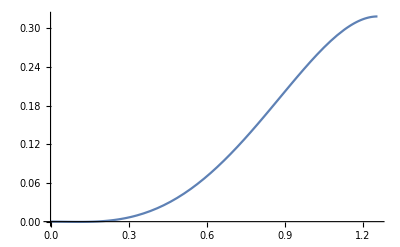

```mathematica
Plot[0.-0.09897251328678063 x^2+0.6124842908534737 x^3-0.26501149358380977 x^4.5,{x,0, 0.2*2 Pi }]
```

```mathematica
B/. beta-> 0.2 * 2Pi /. delta -> 1/Pi /. eps -> 0 /. pi -> Pi
```

-1.95595+4.24141 x-2.45221 x^2+0.423439 x^3-0.00842621 x^4.5

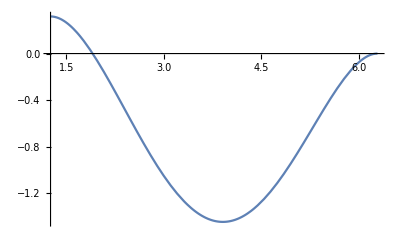

```mathematica
Plot[-1.955951270763495+4.241407143131091 x-2.45220525627579 x^2+0.42343932915006105 x^3-0.008426210927644366 x^4.5,{x,0.2 * 2 Pi,2 Pi}]
```

```mathematica
Manipulate[Plot[lambda(x^4-2x^3+x^2)+gamma, {x,0,1}], {lambda, -2,2}, {gamma,-2,2}]
```

```mathematica
Manipulate[Plot[tau(3x^5-10x^3+7.5x^2-0.5x)+lambda(x^4-2x^3+x^2)+gamma, {x,0,1}],{tau, -2,2}, {lambda, -2,2}, {gamma,-2,2}]
```

```mathematica
Manipulate[Plot[kappa(x^6-5x^3+4.5x^2-0.5x)+tau(3x^5-10x^3+7.5x^2-0.5x)+lambda(x^4-2x^3+x^2)+gamma, {x,0,1}],{kappa, -5,5},{tau, -2,2}, {lambda, -2,2}, {gamma,-2,2}]
```

```mathematica
Solve[{6x^5-15x^2+9x-0.5}=={0}]
```

{{x→-0.850132-1.20275 ⅈ},{x→-0.850132+1.20275 ⅈ},{x→0.0619516},{x→0.59344},{x→1.04487}}

```mathematica
Solve[{15x^4-30x^2+15x-0.5}=={0}]
```

{{x→-1.62154},{x→0.0359108},{x→0.555925},{x→1.0297}}

```mathematica
Integrate[lambda(kappa(x^6-5x^3+4.5x^2-0.5x)+tau(3x^5-10x^3+7.5x^2-0.5x)+(x^4-2x^3+x^2))+gamma, {x,0,1}]
```

0.+gamma+lambda/30+(kappa lambda)/7+0.25 lambda tau

```mathematica
x^6-5x^3+4.5x^2-0.5x
```

-0.5 x+4.5 x^2-5 x^3+x^6

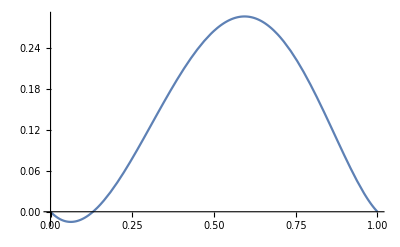

```mathematica
Plot[-0.5 x+4.5 x^2-5 x^3+x^6,{x,0,1}]
```

```mathematica
3x^5-10x^3+7.5x^2-0.5x
```

-0.5 x+7.5 x^2-10 x^3+3 x^5

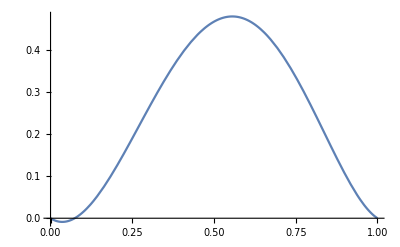

```mathematica
Plot[-0.5 x+7.5 x^2-10 x^3+3 x^5,{x,0,1}]
```

```mathematica
x^4-2x^3+x^2
```

x^2-2 x^3+x^4

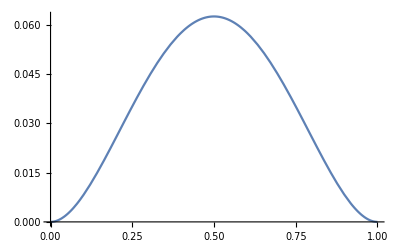

```mathematica
Plot[x^2-2 x^3+x^4,{x,0,1}]
```

```mathematica
lambda(kappa(x^6-5x^3+4.5x^2-0.5x)+tau(3x^5-10x^3+7.5x^2-0.5x)+(x^4-2x^3+x^2))+1-(lambda/30+(kappa lambda)/7+0.25 lambda tau)
```

1-lambda/30-(kappa lambda)/7-0.25 lambda tau+lambda (x^2-2 x^3+x^4+tau (-0.5 x+7.5 x^2-10 x^3+3 x^5)+kappa (-0.5 x+4.5 x^2-5 x^3+x^6))

```mathematica
Manipulate[Plot[1-lambda/30-(kappa lambda)/7-0.25 lambda tau+lambda (x^2-2 x^3+x^4+tau (-0.5 x+7.5 x^2-10 x^3+3 x^5)+kappa (-0.5 x+4.5 x^2-5 x^3+x^6)),{x,0,1
}],{kappa,-1.04,1.04},{lambda,0,2},{tau,-2,2}]
```